```mathematica
data = Import["FreeDynamics_FullExtraction.csv"];
headers=First[data];
time=data[[All,First@FirstPosition[headers,"Time"]]];
angleCols = Flatten @ Position[headers, _?(StringContainsQ["fresh"])];
```

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[fresh][List].

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

C:\Users\mogue\OneDrive\Escritorio\Pringle data\Relaxation dynamics

```mathematica
(*Function for extracting damped period*)
frequency[values_,n_]:= ( 1/(#1 / #2)  &)[values,n];
```

Plotting all the data trajectories. Younger ones seem to asymptote right away, suggesting overdamped behavior ( < 96.1 hrs). Older ones start oscillating a little bit.

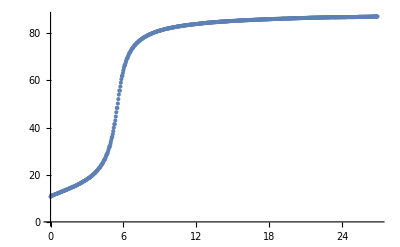
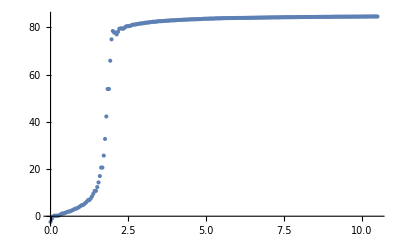
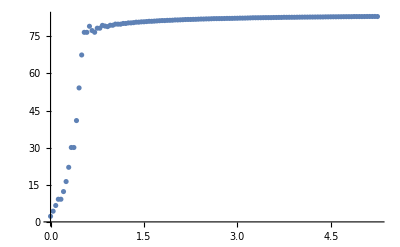
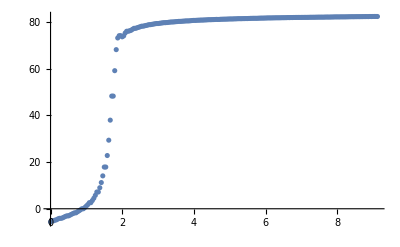
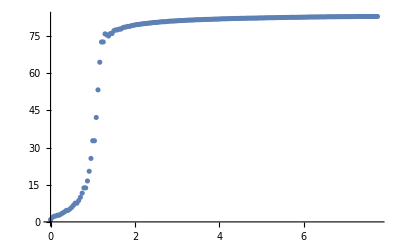
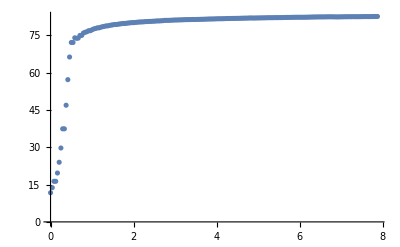
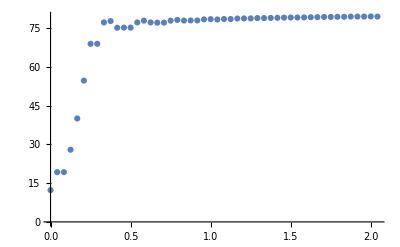
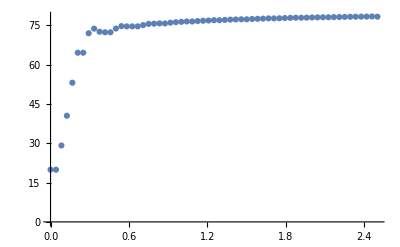

```mathematica
PlotsExp=Table[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, n]]]}], PlotRange->All],{n, 1, 38,1}];
PlotsExp
```

Following the pendulum model, the wiggling indicates damped oscillations about a rest state. We can extract damping coefficients from the exponential envelope. We take 5 points on the envelope to fit an exponential function y[x] = A Exp[-(t-t_0)/τ] +  c/2 using the FindFit function, where c gives the asymptote.

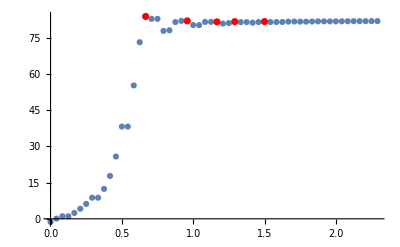

```mathematica
(*Sample 12 -> 96.1 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[17]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[24]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[29]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[32]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[37]]}, PlotStyle->Red]
]
```

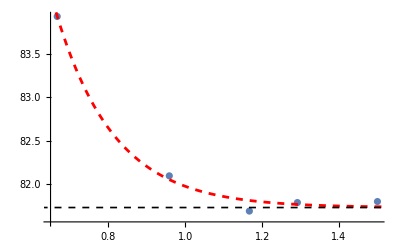

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[17]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[24]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[29]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[32]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[37]]}],
Plot[(A Exp[-(t-Rest[time][[17]]) b]+ c/2)/. {A->2.1973509298431977,b->6.594887092325513,c->163.46391704944412},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->163.46391704944412, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[37]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[17]])[[1]], 4]
```

4.8

```mathematica
(*sample 13 -> age 96.2 hrs*)
```

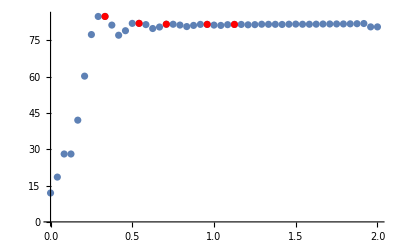

```mathematica
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[9]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[14]], Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[24]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[28]]}, PlotStyle->Red]]
```

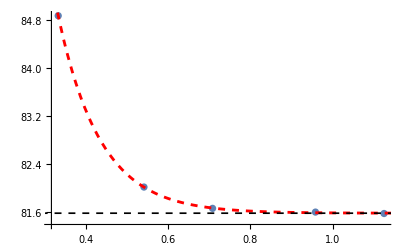

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[9]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[14]], Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[24]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[28]]}],
Plot[(A Exp[-(t-0.333333333) b]+ c/2)/. {A->3.291621612934128,b->9.7221433282357,c->163.16997101886759},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->163.16997101886759, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[28]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 13]]]}][[9]])[[1]], 4]
```

5.05263

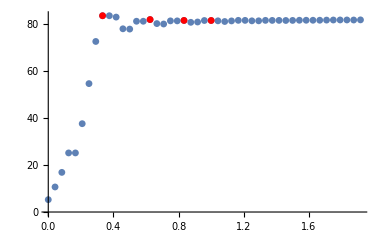

```mathematica
(*Sample 14 -> 96.3 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[9]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[16]], Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[21]] ,Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[25]]}, PlotStyle->Red]]
```

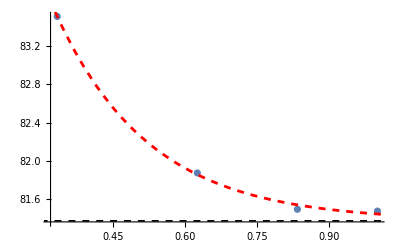

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[9]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[16]], Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[21]] ,Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[25]]}],
Plot[(A Exp[-(t-0.333333333) b]+ c/2)/. {A->2.1332298768257663,b->5.096804704383117,c->162.75414453752123},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->162.75414453752123, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[25]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 14]]]}][[9]])[[1]], 3]
```

4.5

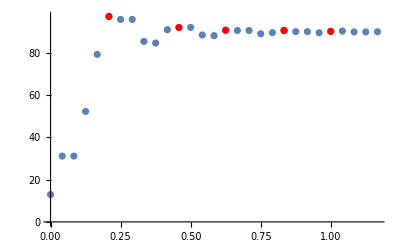

```mathematica
(*sample 18 -> 120.1 hrs (CHOSEN ONE FOR SI)*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[6]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[12]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[25]]}, PlotStyle->Red]]
```

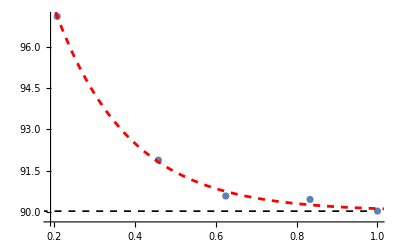

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[6]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[12]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[25]]}],
Plot[(A Exp[-(t-0.208333333) b]+ c/2)/. {A->7.063620839003796,b->5.498529842513505,c->180.0611519889982},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->180.0611519889982, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[25]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 18]]]}][[6]])[[1]], 4]
```

5.05263

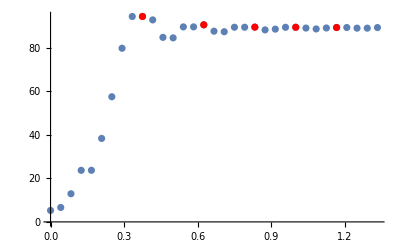

```mathematica
(*Sample 19 -> 120.2 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[25]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[29]]}, PlotStyle->Red]
]
```

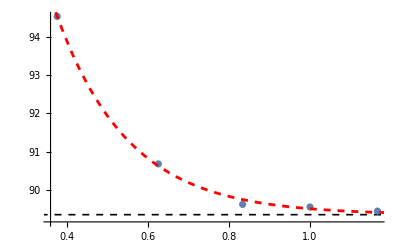

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[25]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[29]]}],
Plot[(A Exp[-(t-0.375) b]+ c/2)/. {A->5.181041706861317,b->5.617908553316073,c->178.7017846655297},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->178.7017846655297, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[29]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 19]]]}][[10]])[[1]], 4]
```

5.05263

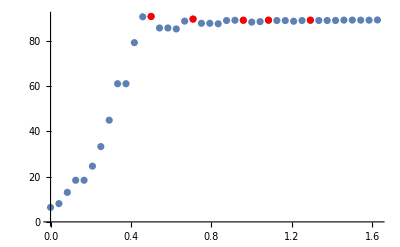

```mathematica
(*Sample 20 -> 120.3 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[24]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[27]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[32]]}, PlotStyle->Red]
]
```

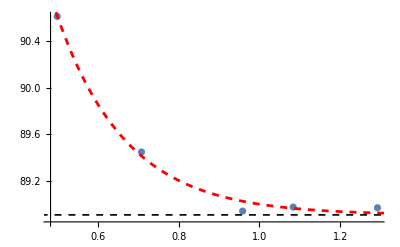

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[24]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[27]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[32]]}],
Plot[(A Exp[-(t-0.5) b]+ c/2)/.{A->1.7094769646757824,b->5.844658432745917,c->177.81831836095475},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->177.81831836095475, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[32]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 20]]]}][[13]])[[1]], 4]
```

5.05263

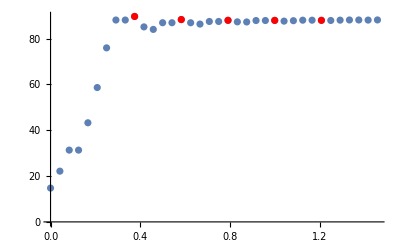

```mathematica
(*Sample 21 -> 120.4 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[25]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[30]]}, PlotStyle->Red]
]
```

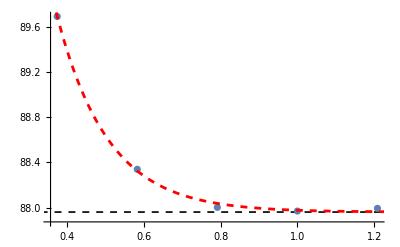

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[25]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[30]]}],
Plot[(A Exp[-(t-0.375) b]+ c/2)/.{A->1.7297530292833092,b->7.493640260247429,c->175.92360524344625},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->175.92360524344625, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[30]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 21]]]}][[10]])[[1]], 4]
```

4.8

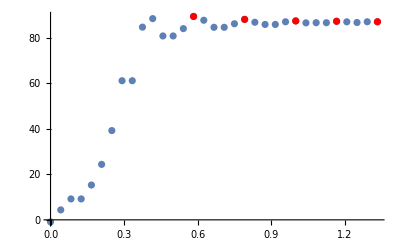

```mathematica
(*Sample 25 -> 144.1 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[25]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[29]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[33]],}, PlotStyle->Red]
]
```

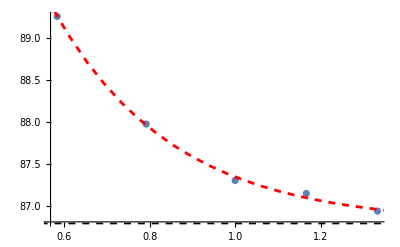

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[25]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[29]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[33]]}],
Plot[(A Exp[-(t-0.583333333) b]+ c/2)/.{A->2.476862105766373,b->3.5794026797845375,c->173.57578967959756},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->173.57578967959756, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[33]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 25]]]}][[15]])[[1]], 4]
```

5.33333

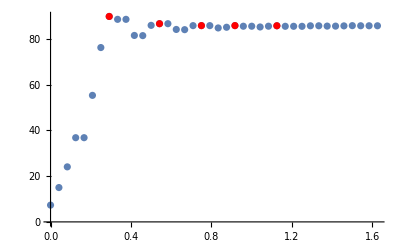

```mathematica
(*Sample 26 ->  144.2 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[8]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[14]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[19]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[23]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[28]]}, PlotStyle->Red]
]
```

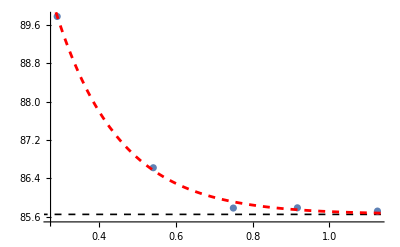

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[8]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[14]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[19]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[23]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[28]]}],
Plot[(A Exp[-(t-0.291666667) b]+ c/2)/.{A->4.1376926022480545,b->6.0130013594923,c->171.29603875982653},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->171.29603875982653, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[28]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 26]]]}][[8]])[[1]], 4]
```

4.8

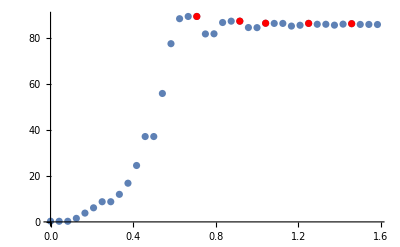

```mathematica
(*Sample 27 ->  144.3 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[23]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[26]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[31]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[36]]}, PlotStyle->Red]
]
```

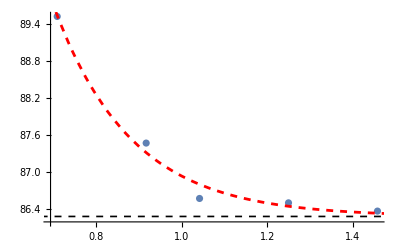

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[23]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[26]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[31]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[36]]}],Plot[(A Exp[-(t-0.708333333) b]+ c/2)/.{A->3.252283543390434,b->5.503602973610219,c->172.56433085930115},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->172.56433085930115, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[36]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 27]]]}][[18]])[[1]], 4]
```

5.33333

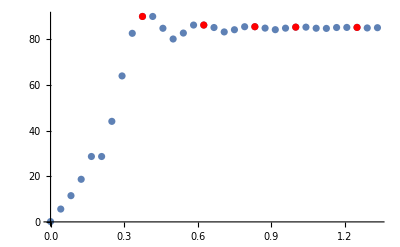

```mathematica
(*Sample 28 -> 144.4 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[25]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[31]]}, PlotStyle->Red]
]
```

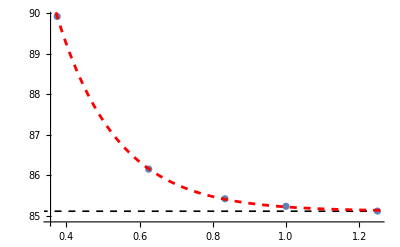

```mathematica
Show[
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[25]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[31]]}],Plot[(A Exp[-(t-0.375) b]+ c/2)/.{A->4.795049055285837,b->6.093999183061484,c->170.23896109644582},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->170.23896109644582, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[31]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 28]]]}][[10]])[[1]], 4]
```

4.57143

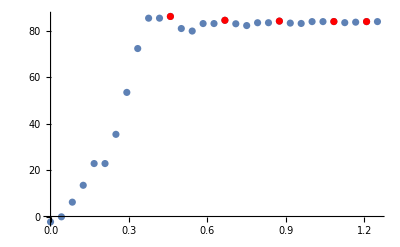

```mathematica
(*29 sample -> 144.5 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[12]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[17]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[27]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[30]]}, PlotStyle->Red]
]
```

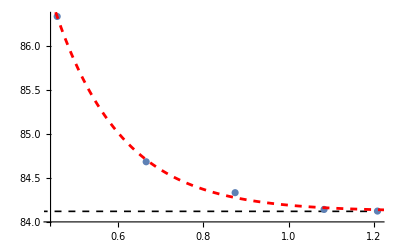

```mathematica
Show[
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[12]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[17]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[27]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[30]]}],Plot[(A Exp[-(t-Rest[time][[12]]) b]+ c/2)/.{A->2.2133692469887483,b->6.363674909172996,c->168.23237892858472},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->168.23237892858472, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[30]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 29]]]}][[12]])[[1]], 4]
```

5.33333

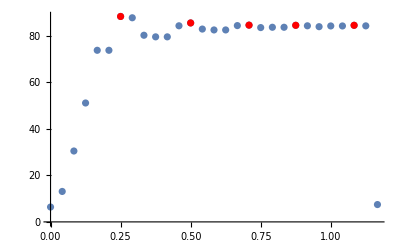

```mathematica
(*30 sample -> 144.6 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[7]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[27]]}, PlotStyle->Red]
]
```

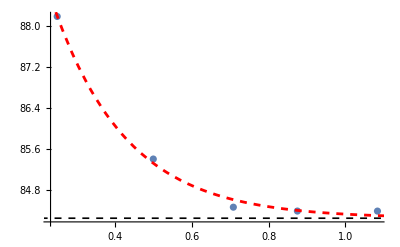

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[7]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[27]]}],
Plot[(A Exp[-(t-Rest[time][[7]]) b]+ c/2)/.{A->3.9459222544455037,b->5.209218956125442,c->168.51565954698737},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->168.51565954698737, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[27]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 30]]]}][[7]])[[1]], 4]
```

4.8

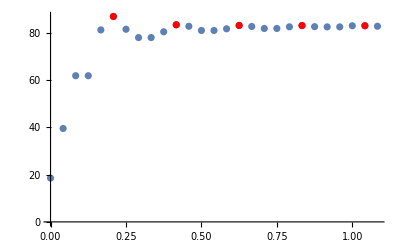

```mathematica
(*31 sample -> 144.7 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[6]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[11]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[26]]}, PlotStyle->Red]
]
```

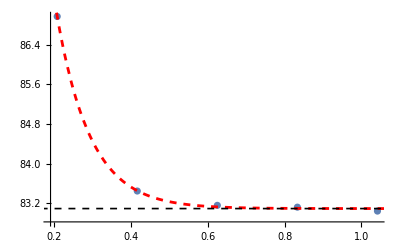

```mathematica
Show[
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[6]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[11]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[16]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[21]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[26]]}],Plot[(A Exp[-(t-Rest[time][[6]]) b]+ c/2)/.{A->3.8747513299261915,b->11.399715824434914,c->166.190441042818},{t, -2, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->166.190441042818, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[26]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 31]]]}][[6]])[[1]], 4]
```

4.8

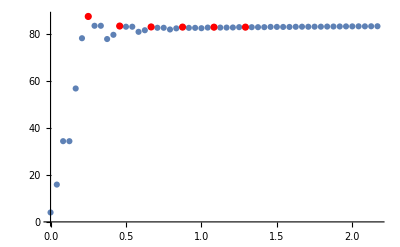

```mathematica
(*32 sample -> 144.8 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[7]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[12]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[17]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[27]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[32]]}, PlotStyle->Red]
]
```

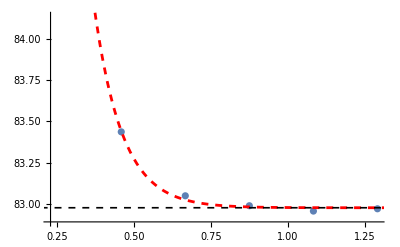

```mathematica
Show[
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[7]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[12]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[17]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[27]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[32]]}],Plot[(A Exp[-(t-Rest[time][[7]]) b]+ c/2)/.{A->4.5417407398079295,b->10.915290183862963,c->165.9491027677205},{t, 0, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->165.9491027677205, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 32]]]}][[32]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 12]]]}][[7]])[[1]], 4]
```

3.84

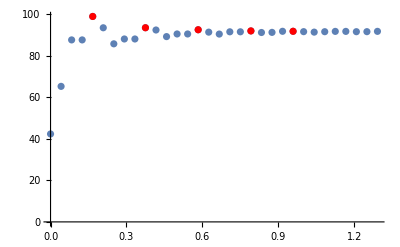

```mathematica
(*33 sample -> 168.1 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[5]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[24]]
}, PlotStyle->Red]
]
```

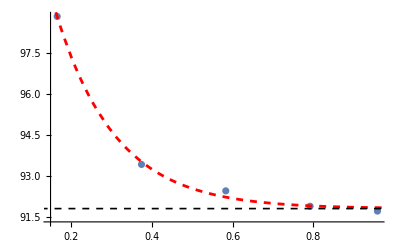

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[5]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[24]]
}],
Plot[(A Exp[-(t-Rest[time][[5]]) b]+ c/2)/.{A->7.03338466570078,b->6.7617197472699075,c->183.58911393271575},{t, -2, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->183.58911393271575, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[24]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 33]]]}][[5]])[[1]], 4]
```

5.05263

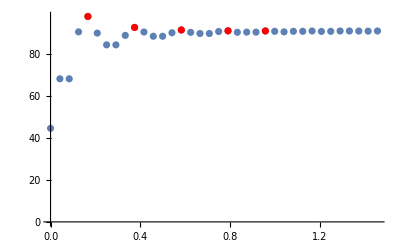

```mathematica
(*34 sample -> 168.2 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[5]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[24]]}, PlotStyle->Red]
]
```

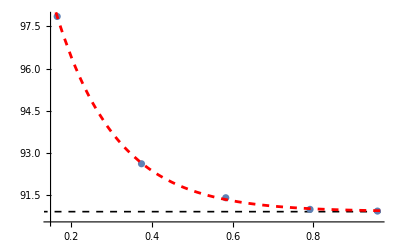

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[5]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[20]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[24]]}],Plot[(A Exp[-(t-Rest[time][[5]]) b]+ c/2)/.{A->6.923579428185456,b->6.670043104630318,c->181.8428568018427},{t, -2, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->181.8428568018427, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[24]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 34]]]}][[5]])[[1]], 4]
```

5.05263

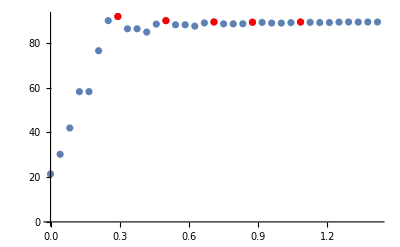

```mathematica
(*36 sample -> 168.4 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[8]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[27]]}, PlotStyle->Red]
]
```

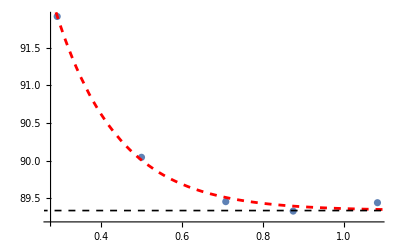

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[8]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[22]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[27]]}],Plot[(A Exp[-(t-Rest[time][[8]]) b]+ c/2)/.{A->2.585829126187223,b->6.476042330628748,c->178.67177896991643},{t, -2, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->178.67177896991643, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[27]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 36]]]}][[8]])[[1]], 4]
```

5.05263

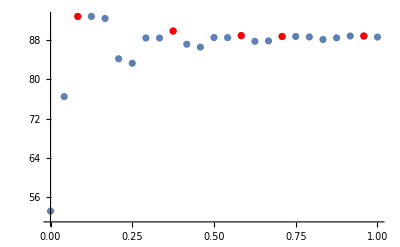

```mathematica
(*37 sample -> 168.5 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[3]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[24]]}, PlotStyle->Red]
]
```

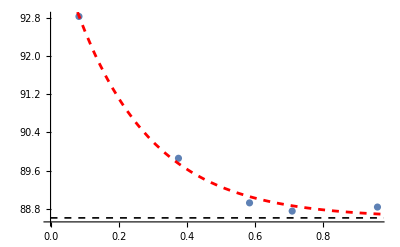

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[3]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[10]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[15]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[18]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[24]]}],Plot[(A Exp[-(t-Rest[time][[3]]) b]+ c/2)/.{A->4.220413765518654,b->4.4999703057496445,c->177.2294401370988},{t, -2, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->177.2294401370988, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[24]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 37]]]}][[3]])[[1]], 4]
```

4.57143

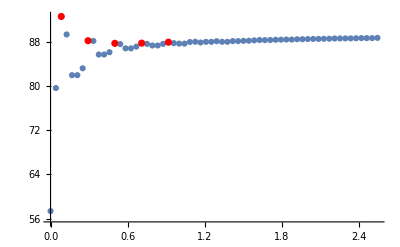

```mathematica
(*38 sample -> 168.6 hrs*)
Show[ListPlot[Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}], PlotRange->All],
ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[3]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[8]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[18]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[23]]}, PlotStyle->Red]
]
```

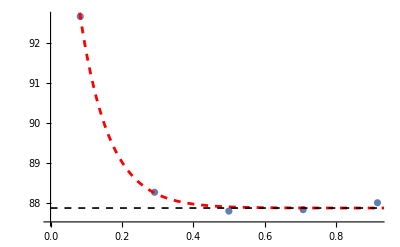

```mathematica
Show[ListPlot[{Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[3]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[8]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[13]],Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[18]],
Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[23]]}],Plot[(A Exp[-(t-Rest[time][[3]]) b]+ c/2)/.{A->4.795094907851771,b->12.206611358026839,c->175.72354533034684},{t, -2, 2}, PlotStyle->{Red, Dashed, Thickness[0.005]}],
Plot[ c/2/.c->175.72354533034684, {t, 0 , 2},PlotStyle->{Black, Dashed, Thickness[0.003]}]
]
```

```mathematica
frequency[(Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[23]]-Transpose[{Rest[time], Rest[data[[All, angleCols]][[All, 38]]]}][[3]])[[1]], 4]
```

4.8